```mathematica
description="El Mu -> El Mu, QED, matrix element squared, tree";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];

(*Generate Feynman Diagrams*)
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
```

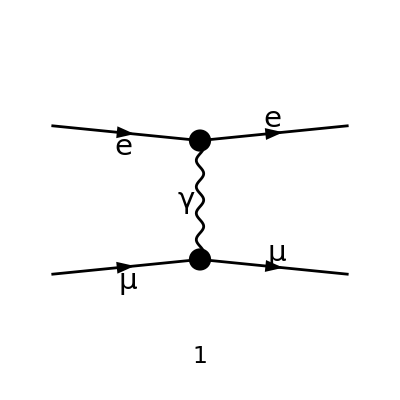

-(e^2 (φ(OverBar[p3],m_e)).(γ̄)^Lor2.(φ(OverBar[p_1],m_e)) (φ(OverBar[p4],m_μ)).(γ̄)^Lor2.(φ(OverBar[p_2],m_μ)))/(OverBar[p4]-OverBar[p_2])^2

Results are equal.

CPU Time used: 2.704 s.

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[2,{1}],F[2,{2}]}->{F[2,{1}],F[2,{2}]},InsertionLevel->{Classes},Restrictions->QEDOnly];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];

(*MatrixElement*)
M[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True]

(*Fix the Kinematics*)
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,SMP["m_e"],SMP["m_mu"],SMP["m_e"],SMP["m_mu"]];

(*Square the Amplitude*)
MSquared[0]=Simplify[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[FeynAmpDenominatorExplicit[M[0]*ComplexConjugate[M[0]]]]]];


(*Evaluate the matrix element*)
matrixElement=I*(SpinorUBar[p3,SMP["m_e"]].I.SMP["e"].GA[lambda].SpinorU[p1,SMP["m_e"]])*(-I.MetricTensor[lambda,sigma]/SP[p3-p1])*(SpinorUBar[p4,SMP["m_mu"]].I.SMP["e"].GA[sigma].SpinorU[p2,SMP["m_mu"]])//Simplify//Contract;

FeyncalcResult=Simplify[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[FeynAmpDenominatorExplicit[matrixElement*ComplexConjugate[matrixElement]]]]];

resultA=MSquared[0];
resultB=FeyncalcResult;

comparison=FullSimplify[resultA==resultB];

If[comparison,
Print["Results are equal."],Print["Results are not equal."]]
Print["\tCPU Time used: ",Round[N[TimeUsed[],3],0.001]," s."];
```